```mathematica
Needs["PlotLegends`"]
```

LegendShadow::shdw: Symbol "LegendShadow" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

```mathematica
nmax = 15;
α = 0.6;
c = 2.997 10^8;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
ω = c 2 Pi/λ;
λLat = 532 10^-9;
Γ = 1.84 10^6;
ωLat = c * 2 Pi / (λLat);
IntensityLat = 1 /(10^-4);(*from other simulation*)
kb = 1.38066 10^-23;
ω0 = 1.3 10^6;
Ωfree = 2 Pi 30.6 10^3;
ΩRm1 = Sqrt[2 Pi 30.6 10^3];
ΩRm2 = Sqrt[2 Pi 30.6 10^3];
ΔRm = 10^9;
ΔR = 10^12;
(*lattice params*)
a = 532 10^-9;
σ = 0.1 *3 * (265 10^-12)^2/(2 Pi);
ρ = 1/a^2;
RCs = 500;
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
Clear[P1list,P2list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
(*alpha factor to be guessed /measured*)
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
Int = 0.6 10^-3/(10^-4);
h = 2 Pi *hbar;
;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];

H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[4 10^-5  ]] == Re[fun3[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
AppendTo[P1list, Re[fun1[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P2list, Re[fun2[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P3list, Re[fun3[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
{n,lam},{n,0,15}]
Γscatt = tab[[All, 2]]
P1list
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,71289.},{2,141868.},{3,208622.},{4,269385.},{5,321625.},{6,362704.},{7,391025.},{8,407470.},{9,414540.},{10,415504.},{11,412956.},{12,408538.},{13,403115.},{14,397096.},{15,390631.}}

{0,71289.,141868.,208622.,269385.,321625.,362704.,391025.,407470.,414540.,415504.,412956.,408538.,403115.,397096.,390631.}

{1.,0.913446,0.834965,0.762834,0.695124,0.633053,0.580301,0.538549,0.505567,0.47784,0.453576,0.43312,0.417708,0.408214,0.404587,0.405863}

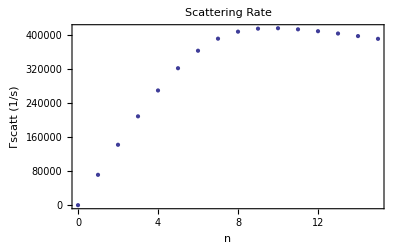

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
(Plots: Scattering Rate As a Function of Raman and Repump Coupling strengths.)
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-5}, MaxSteps-> 1000000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[8 10^-5  ]] == Re[fun[5 10^-5 ]] Exp[-l  3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{ΩR,lam},{ΩR,0,4 10^6, 0.5 10^5}],{n,0,15}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

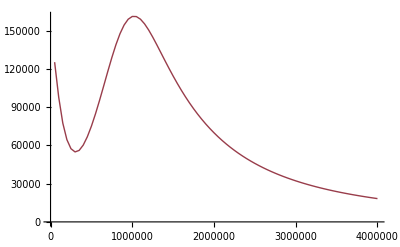
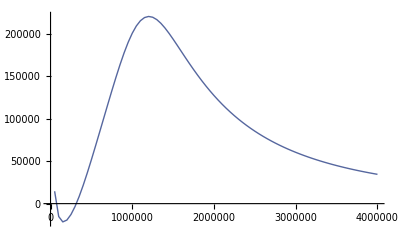
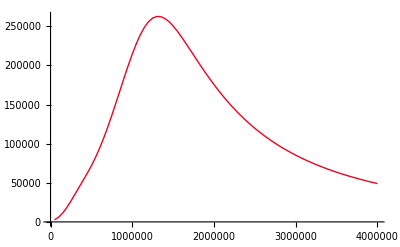
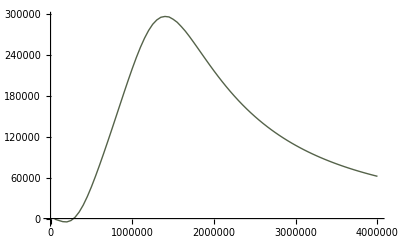
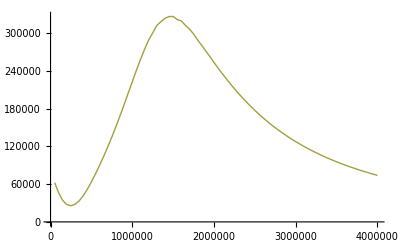
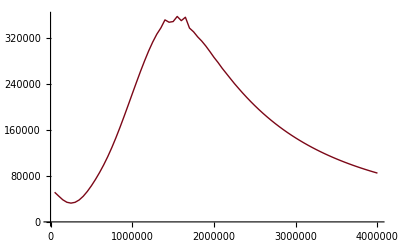
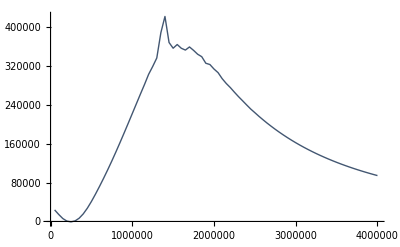
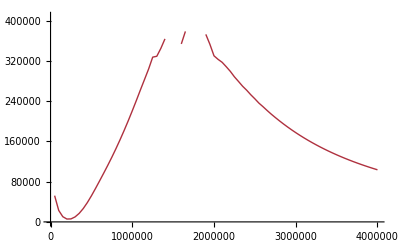

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

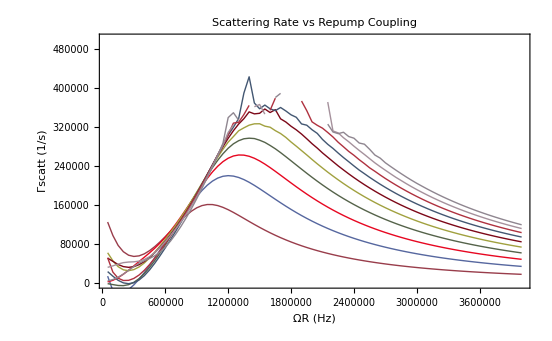

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[10 10^-5  ]] == Re[fun[3 10^-5 ]] Exp[-l  7 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,0,15}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

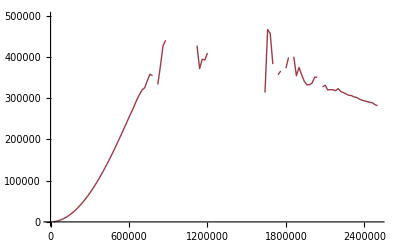
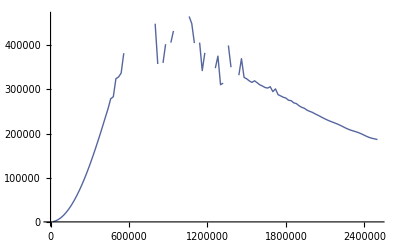
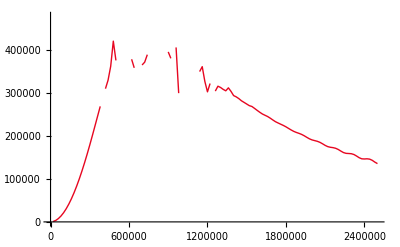
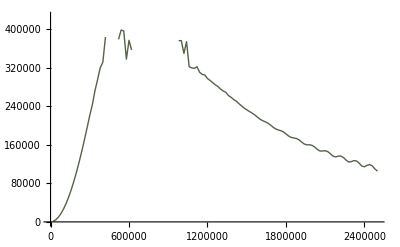
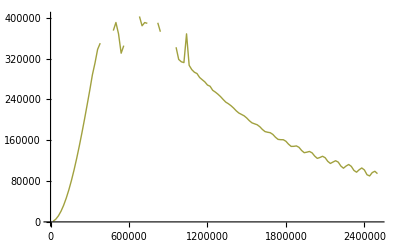
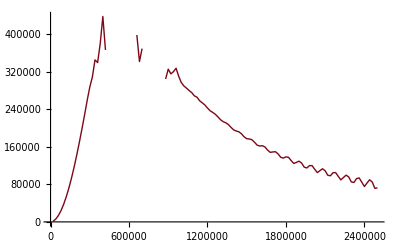
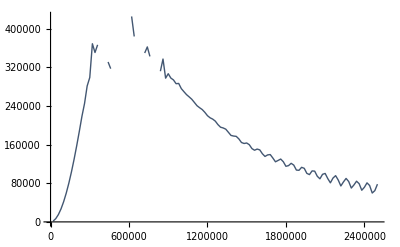
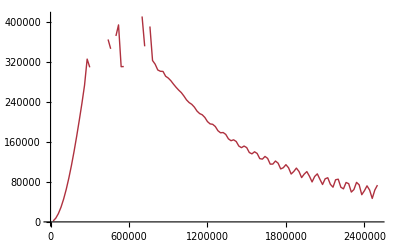

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

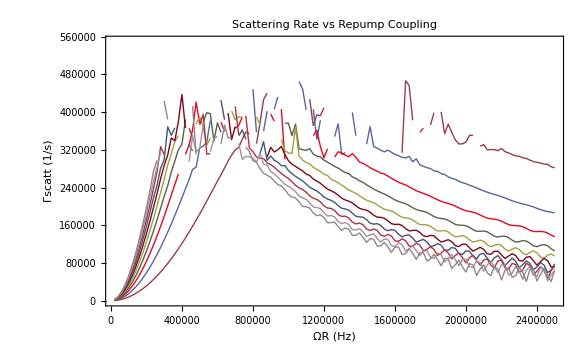

```mathematica
Show[ramanplots , PlotRange -> {All,{0,550000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
Photon recoil
```

```mathematica
Γscatt;
pphoton = h / λ;
mCs = 132.90545 * 1.660539 10^-27 ;(*internet*)
Erecoil = pphoton^2/(2mCs);

Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3;
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,16.5009,32.8374,48.2884,62.3531,74.4447,83.9529,90.5082,94.3148,95.9513,96.1743,95.5845,94.562,93.3067,91.9135,90.4171}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
Ephoton = h * c/λ;
ΛscRm =Table[ Γ    (ΩRm1^2 + ΩRm2^2)/(4 ΔRm^2) Ephoton ,{n,0,15}] 2/(3 kb)10^3
```

{3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Ephoton 2/(3 kb)10^3
```

{24.2951,22.1923,20.2856,18.5331,16.8881,15.3801,14.0985,13.0841,12.2828,11.6092,11.0197,10.5227,10.1482,9.91759,9.82949,9.86048}

```mathematica
Lattice beams
```

```mathematica
(*ephoton not precise, should be average over all resonances*)
(*numerical value taken from last weeks simulartion*)
```

```mathematica
ΛscLat =  Table[1.00217872738179 10^-9 * IntensityLat 2*hbar ω 2/(3 kb) *10^3 ,{n,0,15}]
```

{421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ω1 (1-0.5 η^2(2n+1)),{n,0,15}];
Λcarrier = Table[P1list[[n+1]] ΩR^2/Γ Ωcarrier[[n+1]]^2/(4 ω0^2),{n,0,15}]2*Erecoil 2/(3 kb) *10^3
```

{8.85139,7.43872,6.23322,5.1998,4.30774,3.54968,2.92871,2.4321,2.02967,1.69288,1.40626,1.16401,0.962436,0.796091,0.657764,0.540139}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ω1 (Sqrt[n+1]),{n,0,15}]//N;

Λblue= Table[P1list[[n+1]] ΩR^2/Γ Ωblue[[n+1]]^2/(16 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{32.9478,60.1922,82.5309,100.535,114.514,125.146,133.838,141.952,149.916,157.438,164.388,171.245,178.913,188.297,199.954,213.957}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωcarrier[[1]]*η^2*Sqrt[(n-1)*n],{n,0,15}]//N;

Λdoublyred = -Table[P1list[[n+1]] ΩR^2/Γ Ωdoublyred[[n+1]]^2/(4 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{0.,0.,-0.338187,-0.926916,-1.68928,-2.56407,-3.5256,-4.58072,-5.73357,-6.96745,-8.26706,-9.64851,-11.1662,-12.8965,-14.9122,-17.2607}

```mathematica
Rescattering
```

```mathematica
Λresc = Table[(P1list[[n+1]]α+P2list[[n+1]](1-α)) 1.00217872738179 10^9 (σ ρ)/2 Log[RCs],{n,0,15}]*2/(3 kb) *10^3 *2* Erecoil
```

{0.0170786,0.0156004,0.01426,0.0130282,0.0118718,0.0108117,0.00991074,0.00919768,0.00863438,0.00816085,0.00774645,0.0073971,0.00713387,0.00697173,0.00690979,0.00693158}

```mathematica
Repumping of state 2
```

```mathematica
Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);
ΛRepump = Table[P2list[[n+1]] * Γ2s *2* Erecoil,{n,0,15}] 2/(3 kb) *10^3
```

{0.,30.547,56.9323,80.5405,102.504,122.793,141.094,158.036,174.687,191.212,206.599,219.454,228.815,234.491,236.99,237.26}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n+1]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,0,15}] 2/(3 kb) *10^3 hbar ω0;
Λcool[[1]] = 0;
Λcool
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{0,-446.61,-807.235,-1087.28,-1298.4,-1439.96,-1498.52,-1471.53,-1381.71,-1263.78,-1144.09,-1033.69,-933.124,-839.19,-749.113,-661.885}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 0","n=1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp ,Λresc,ΛscLat, Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λresc","ΛscLat","Λdoublyred","Λcool"}}];
Grid[TableOfValues2[[All,{1,2,3,6,8,10,12}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 0 | n=1 | n=4 | n=6 | n=8 | n=10
Λrecarate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λrecerate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λcarrier | 8.85139 | 7.43872 | 4.30774 | 2.92871 | 2.02967 | 1.40626
Λblue | 32.9478 | 60.1922 | 114.514 | 133.838 | 149.916 | 164.388
ΛscRm | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234
ΛscRp | 24.2951 | 22.1923 | 16.8881 | 14.0985 | 12.2828 | 11.0197
Λresc | 0.0170786 | 0.0156004 | 0.0118718 | 0.00991074 | 0.00863438 | 0.00774645
ΛscLat | 421.916 | 421.916 | 421.916 | 421.916 | 421.916 | 421.916
Λdoublyred | 0. | 0. | -1.68928 | -3.5256 | -5.73357 | -8.26706
Λcool | 0 | -446.61 | -1298.4 | -1498.52 | -1381.71 | -1144.09

```mathematica
Rate equation
```

```mathematica
Matrix Elements (from seperate notebook)
```

```mathematica
Matd ={{1.308569897893965+0. ⅈ,0.19862052313093037+0. ⅈ,0.027226899926630355+0. ⅈ,0.004138097078535725+0. ⅈ,0.0007391015056127313+0. ⅈ,0.00015007944035278273+0. ⅈ,0.000033694733319029394+0. ⅈ,8.224120911688334*^-6+0. ⅈ,2.1549081564532717*^-6+0. ⅈ,6.00229492190712*^-7+0. ⅈ,1.763624284202687*^-7+0. ⅈ,5.432437701688166*^-8+0. ⅈ,1.7450408188768573*^-8+0. ⅈ,5.812392895961771*^-9+0. ⅈ,1.9752381560801494*^-9+0. ⅈ,6.820406700870345*^-10+0. ⅈ},{0.19867979838976085+0. ⅈ,1.1543591971155138+0. ⅈ,0.24919233195856547+0. ⅈ,0.04355537323937796+0. ⅈ,0.007781700973826577+0. ⅈ,0.0015730398982837794+0. ⅈ,0.0003533575943409387+0. ⅈ,0.0000862611518641107+0. ⅈ,0.00002260113618099127+0. ⅈ,6.295313160211243*^-6+0. ⅈ,1.8497288260997286*^-6+0. ⅈ,5.697660902594574*^-7+0. ⅈ,1.8302367885661115*^-7+0. ⅈ,6.096164643218775*^-8+0. ⅈ,2.0716729831209444*^-8+0. ⅈ,7.153391648429841*^-9+0. ⅈ},{0.027199297344761775+0. ⅈ,0.2492061076962415+0. ⅈ,1.02897633085769+0. ⅈ,0.28449990928551394+0. ⅈ,0.05970132502308163+0. ⅈ,0.012096966580498669+0. ⅈ,0.0027010073800715776+0. ⅈ,0.0006597760232712002+0. ⅈ,0.00017291508491735442+0. ⅈ,0.000048159853140269514+0. ⅈ,0.000014150500052842484+0. ⅈ,4.358767176591439*^-6+0. ⅈ,1.4001490361599327*^-6+0. ⅈ,4.6636222632001474*^-7+0. ⅈ,1.5848491381888152*^-7+0. ⅈ,5.472411619828041*^-8+0. ⅈ},{0.004135383554589816+0. ⅈ,0.04355683766756279+0. ⅈ,0.28449986046463366+0. ⅈ,0.9286849695279454+0. ⅈ,0.3082320494925438+0. ⅈ,0.07495340372823922+0. ⅈ,0.016822184315267823+0. ⅈ,0.00407693130145825+0. ⅈ,0.0010691978833738513+0. ⅈ,0.00029792014480273563+0. ⅈ,0.00008752646052961672+0. ⅈ,0.000026960157791947873+0. ⅈ,8.660407326729051*^-6+0. ⅈ,2.8846131149807102*^-6+0. ⅈ,9.80283229976637*^-7+0. ⅈ,3.384873590433936*^-7+0. ⅈ},{0.0007385991530855627+0. ⅈ,0.007781974944389175+0. ⅈ,0.05970131304602746+0. ⅈ,0.3082320500120408+0. ⅈ,0.8475752149664059+0. ⅈ,0.323789226979997+0. ⅈ,0.08911042959915053+0. ⅈ,0.021789140531999183+0. ⅈ,0.005657588885974309+0. ⅈ,0.0015774177751758354+0. ⅈ,0.0004637342069455229+0. ⅈ,0.000142821012476286+0. ⅈ,0.00004587659752169408+0. ⅈ,0.000015280878308164143+0. ⅈ,5.192937261944276*^-6+0. ⅈ,1.7930938046559165*^-6+0. ⅈ},{0.00014997589502452135+0. ⅈ,0.0015730958723446905+0. ⅈ,0.012096964461639569+0. ⅈ,0.07495340380329599+0. ⅈ,0.32378922697852863+0. ⅈ,0.781146470572157+0. ⅈ,0.33338084546688806+0. ⅈ,0.10211370616587911+0. ⅈ,0.026878290336102634+0. ⅈ,0.007402197778828042+0. ⅈ,0.002177167446068167+0. ⅈ,0.0006711517248570684+0. ⅈ,0.00021555008658503567+0. ⅈ,0.00007179198779233437+0. ⅈ,0.000024397857082481207+0. ⅈ,8.42448658394921*^-6+0. ⅈ},{0.00003367156961236691+0. ⅈ,0.0003533701300318214+0. ⅈ,0.002701006896895162+0. ⅈ,0.01682218433304713+0. ⅈ,0.08911042959860935+0. ⅈ,0.33338084546688884+0. ⅈ,0.7262158106871403+0. ⅈ,0.3385373869864518+0. ⅈ,0.1139757225645587+0. ⅈ,0.03200709378146649+0. ⅈ,0.00927484508057386+0. ⅈ,0.0028596299006221904+0. ⅈ,0.0009196008394281947+0. ⅈ,0.0003062306320721271+0. ⅈ,0.00010405816672656895+0. ⅈ,0.00003593208638047529+0. ⅈ},{8.218468868378262*^-6+0. ⅈ,0.00008626421147570801+0. ⅈ,0.0006597759047921094+0. ⅈ,0.004076931305816172+0. ⅈ,0.021789140531885753+0. ⅈ,0.1021137061658776+0. ⅈ,0.3385373869864424+0. ⅈ,0.6804546589301799+0. ⅈ,0.3403570622615889+0. ⅈ,0.12474032184316747+0. ⅈ,0.0371193316668172+0. ⅈ,0.011244821510495377+0. ⅈ,0.0036148513749477925+0. ⅈ,0.0012058496111424712+0. ⅈ,0.00040968044696525473+0. ⅈ,0.00014144217201751653+0. ⅈ},{2.153426809339535*^-6+0. ⅈ,0.00002260193799292065+0. ⅈ,0.00017291505391944944+0. ⅈ,0.0010691978845112392+0. ⅈ,0.005657588885936844+0. ⅈ,0.026878290336067135+0. ⅈ,0.11397572256439464+0. ⅈ,0.340357062261073+0. ⅈ,0.6421083604249234+0. ⅈ,0.3396516927613679+0. ⅈ,0.13446295901933078+0. ⅈ,0.042176595628871265+0. ⅈ,0.013284561062944875+0. ⅈ,0.004426467063642455+0. ⅈ,0.00150726920852579+0. ⅈ,0.0005203049808782057+0. ⅈ},{5.998168835327144*^-7+0. ⅈ,6.2955364933932616*^-6+0. ⅈ,0.00004815984451046094+0. ⅈ,0.0002979201451412756+0. ⅈ,0.001577417775280534+0. ⅈ,0.007402197779359161+0. ⅈ,0.0320070937836896+0. ⅈ,0.12474032185244296+0. ⅈ,0.3396516928008053+0. ⅈ,0.6098209876757755+0. ⅈ,0.3370361893578362+0. ⅈ,0.14319915588719584+0. ⅈ,0.047146261696754524+0. ⅈ,0.015349497897681514+0. ⅈ,0.0052148109232741735+0. ⅈ,0.0018052483605646955+0. ⅈ},{1.7624119586086676*^-7+0. ⅈ,1.8497944480710432*^-6+0. ⅈ,0.00001415049752957239+0. ⅈ,0.00008752646070762789+0. ⅈ,0.0004637342073926593+0. ⅈ,0.002177167448180516+0. ⅈ,0.009274845089396116+0. ⅈ,0.03711933170348682+0. ⅈ,0.13446295918323173+0. ⅈ,0.33703618930405654+0. ⅈ,0.5825198571436385+0. ⅈ,0.3329793336708261+0. ⅈ,0.15098003526165696+0. ⅈ,0.05193283706581885+0. ⅈ,0.017194692494969827+0. ⅈ,0.005931881285490663+0. ⅈ},{5.4287027860128984*^-8+0. ⅈ,5.697862393025735*^-7+0. ⅈ,4.358765907119029*^-6+0. ⅈ,0.00002696015480204699+0. ⅈ,0.00014282099648524484+0. ⅈ,0.0006711516497450346+0. ⅈ,0.002859629579877632+0. ⅈ,0.01124482024720184+0. ⅈ,0.04217659107500372+0. ⅈ,0.14319913970205758+0. ⅈ,0.3329792636241044+0. ⅈ,0.5593183900481268+0. ⅈ,0.32778052746512376+0. ⅈ,0.1576140194052254+0. ⅈ,0.055816351017575636+0. ⅈ,0.018716211074459314+0. ⅈ},{1.7438412793924686*^-8+0. ⅈ,1.830301737311558*^-7+0. ⅈ,1.4001488002891897*^-6+0. ⅈ,8.660407429747668*^-6+0. ⅈ,0.00004587659801919498+0. ⅈ,0.00021555008885617866+0. ⅈ,0.0009196008495885644+0. ⅈ,0.003614851431106167+0. ⅈ,0.013284561016952173+0. ⅈ,0.04714625999370548+0. ⅈ,0.1509800924945317+0. ⅈ,0.32778022490378045+0. ⅈ,0.5392686575653952+0. ⅈ,0.3211861692261908+0. ⅈ,0.160953919535107+0. ⅈ,0.05832923107804041+0. ⅈ},{5.809157225163038*^-9+0. ⅈ,6.097178405291724*^-8+0. ⅈ,4.6642314972809195*^-7+0. ⅈ,2.8849904666546843*^-6+0. ⅈ,0.000015282877305541118+0. ⅈ,0.00007180137947310818+0. ⅈ,0.0003062706746638627+0. ⅈ,0.0012060074512825895+0. ⅈ,0.004427049334515773+0. ⅈ,0.015351464246739489+0. ⅈ,0.05193936997779259+0. ⅈ,0.15764210023580771+0. ⅈ,0.3212055276243001+0. ⅈ,0.5186968235767893+0. ⅈ,0.30824740695910313+0. ⅈ,0.16086278205086674+0. ⅈ},{1.9679710894679656*^-9+0. ⅈ,2.0655442233850392*^-8+0. ⅈ,1.5801042413101495*^-7+0. ⅈ,9.773485227385898*^-7+0. ⅈ,5.1773910398729775*^-6+0. ⅈ,0.00002432481754435705+0. ⅈ,0.00010374661396698198+0. ⅈ,0.00040845393594412+0. ⅈ,0.0015027644495779278+0. ⅈ,0.005199151646394474+0. ⅈ,0.01714234699352862+0. ⅈ,0.055659098933787225+0. ⅈ,0.16055024695209286+0. ⅈ,0.305475818673706+0. ⅈ,0.4727787959418403+0. ⅈ,0.31386977463263604+0. ⅈ},{6.864619876311596*^-10+0. ⅈ,7.204971571259486*^-9+0. ⅈ,5.511674233974088*^-8+0. ⅈ,3.4091595333926835*^-7+0. ⅈ,1.8059587801891176*^-6+0. ⅈ,8.484929462031004*^-6+0. ⅈ,0.000036189975504218306+0. ⅈ,0.00014245657998692473+0. ⅈ,0.0005240217978809866+0. ⅈ,0.0018183971577803118+0. ⅈ,0.005975746187668232+0. ⅈ,0.0188183530135478+0. ⅈ,0.058748191045581724+0. ⅈ,0.16531299354752793+0. ⅈ,0.29579598462451856+0. ⅈ,0.24592933171801587+0. ⅈ}};
```

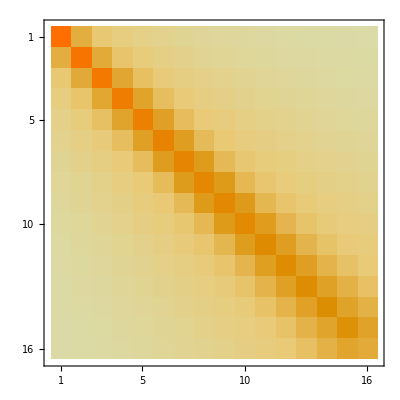

```mathematica
MatrixPlot[Matd]
```

```mathematica
Γheat = 0.1* Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,15}] (*cheated*)
```

{70817.4 α,78987. α,86412.2 α,92969. α,98557.8 α,103119. α,106697. α,109384. α,111287. α,112519. α,113271. α,113783. α,114291. α,114974. α,115929. α,117164. α}

```mathematica
Γeff[n_]:=Γscatt[[n]]
```

Rate Equation

```mathematica
Pm[t_]:= {P0[t],P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]};
Pm'[t]
Pmen = {P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15};
```

{P0'[t],P1'[t],P2'[t],P3'[t],P4'[t],P5'[t],P6'[t],P7'[t],P8'[t],P9'[t],P10'[t],P11'[t],P12'[t],P13'[t],P14'[t],P15'[t]}

```mathematica
Clear[Γeff, Matd, Γheat, α]
```

```mathematica
R = Table[+α(Γeff[n+1]*Matd[[n+1,nt]]+Γheat[[n+1]]*Matd[[n+1,nt+1]]), {n,0,nmax},{nt,0,nmax}] ;
For[i=1,i≤ nmax+1,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat[[i]])];
For[i=1,i≤ nmax+1,i++,R[[i,1]] = α Γheat[[i]]*Matd[[i,1]]];
R[[1,1]] =-(Γeff[1]+ Γheat[[1]]) +  α Γheat[[1]]*Matd[[1,1]];
R //MatrixForm
```

(-9129.41+0. ⅈ | 5063.68+0. ⅈ | 694.129+0. ⅈ | 105.498+0. ⅈ | 18.8428+0. ⅈ | 3.82616+0. ⅈ | 0.859022+0. ⅈ | 0.209668+0. ⅈ | 0.0549378+0. ⅈ | 0.0153024+0. ⅈ | 0.00449623+0. ⅈ | 0.00138496+0. ⅈ | 0.000444885+0. ⅈ | 0.000148183+0. ⅈ | 0.0000503572+0. ⅈ | 0.0000173881+0. ⅈ
5649.52+0. ⅈ | -77358.4+0. ⅈ | 56461.7+0. ⅈ | 11897.3+0. ⅈ | 2084.29+0. ⅈ | 377.58+0. ⅈ | 77.3321+0. ⅈ | 17.5672+0. ⅈ | 4.33235+0. ⅈ | 1.14574+0. ⅈ | 0.32187+0. ⅈ | 0.0953207+0. ⅈ | 0.0295752+0. ⅈ | 0.00956201+0. ⅈ | 0.00319662+0. ⅈ | 0.00108953+0. ⅈ
846.126+0. ⅈ | 10067.6+0. ⅈ | -140493.+0. ⅈ | 96437.7+0. ⅈ | 26074.1+0. ⅈ | 5458.14+0. ⅈ | 1113.73+0. ⅈ | 250.437+0. ⅈ | 61.5398+0. ⅈ | 16.2169+0. ⅈ | 4.53961+0. ⅈ | 1.3401+0. ⅈ | 0.414578+0. ⅈ | 0.13369+0. ⅈ | 0.0446274+0. ⅈ | 0.0151927+0. ⅈ
138.406+0. ⅈ | 1975.43+0. ⅈ | 14974.+0. ⅈ | -197709.+0. ⅈ | 126562.+0. ⅈ | 41090.9+0. ⅈ | 9945.16+0. ⅈ | 2242.13+0. ⅈ | 546.106+0. ⅈ | 143.806+0. ⅈ | 40.2209+0. ⅈ | 11.8583+0. ⅈ | 3.66454+0. ⅈ | 1.18059+0. ⅈ | 0.393884+0. ⅈ | 0.134034+0. ⅈ
26.2061+0. ⅈ | 395.491+0. ⅈ | 3376.06+0. ⅈ | 20585.9+0. ⅈ | -248628.+0. ⅈ | 148483.+0. ⅈ | 55496.2+0. ⅈ | 15176.1+0. ⅈ | 3722.54+0. ⅈ | 970.411+0. ⅈ | 271.414+0. ⅈ | 80.0213+0. ⅈ | 24.7121+0. ⅈ | 7.95727+0. ⅈ | 2.65412+0. ⅈ | 0.902961+0. ⅈ
5.56754+0. ⅈ | 87.3395+0. ⅈ | 752.643+0. ⅈ | 5116.9+0. ⅈ | 26484.1+0. ⅈ | -292015.+0. ⅈ | 163118.+0. ⅈ | 68125.+0. ⅈ | 20703.2+0. ⅈ | 5461.63+0. ⅈ | 1509.26+0. ⅈ | 445.054+0. ⅈ | 137.517+0. ⅈ | 44.2609+0. ⅈ | 14.7598+0. ⅈ | 5.02092+0. ⅈ
1.29335+0. ⅈ | 20.9009+0. ⅈ | 180.649+0. ⅈ | 1233.95+0. ⅈ | 7083.69+0. ⅈ | 32197.8+0. ⅈ | -326276.+0. ⅈ | 171044.+0. ⅈ | 78051.2+0. ⅈ | 26033.1+0. ⅈ | 7321.71+0. ⅈ | 2128.25+0. ⅈ | 657.642+0. ⅈ | 211.888+0. ⅈ | 70.6396+0. ⅈ | 24.0256+0. ⅈ
0.323628+0. ⅈ | 5.3251+0. ⅈ | 46.2196+0. ⅈ | 315.335+0. ⅈ | 1814.52+0. ⅈ | 9133.1+0. ⅈ | 37288.4+0. ⅈ | -350434.+0. ⅈ | 173047.+0. ⅈ | 84764.8+0. ⅈ | 30727.6+0. ⅈ | 9151.54+0. ⅈ | 2780.55+0. ⅈ | 895.582+0. ⅈ | 299.043+0. ⅈ | 101.687+0. ⅈ
0.0862738+0. ⅈ | 1.43199+0. ⅈ | 12.4534+0. ⅈ | 85.1104+0. ⅈ | 488.063+0. ⅈ | 2460.02+0. ⅈ | 11137.5+0. ⅈ | 41500.9+0. ⅈ | -365306.+0. ⅈ | 170592.+0. ⅈ | 88425.8+0. ⅈ | 34563.5+0. ⅈ | 10843.6+0. ⅈ | 3425.18+0. ⅈ | 1142.58+0. ⅈ | 389.346+0. ⅈ
0.0242966+0. ⅈ | 0.404201+0. ⅈ | 3.51665+0. ⅈ | 24.0463+0. ⅈ | 137.996+0. ⅈ | 692.181+0. ⅈ | 3137.61+0. ⅈ | 13013.8+0. ⅈ | 44784.1+0. ⅈ | -372870.+0. ⅈ | 165329.+0. ⅈ | 89629.6+0. ⅈ | 37526.8+0. ⅈ | 12348.2+0. ⅈ | 4029.03+0. ⅈ | 1370.17+0. ⅈ
0.00718665+0. ⅈ | 0.119367+0. ⅈ | 1.03818+0. ⅈ | 7.09685+0. ⅈ | 40.7304+0. ⅈ | 204.389+0. ⅈ | 920.977+0. ⅈ | 3825.87+0. ⅈ | 14737.+0. ⅈ | 47265.4+0. ⅈ | -375689.+0. ⅈ | 158802.+0. ⅈ | 89169.1+0. ⅈ | 39757.4+0. ⅈ | 13648.1+0. ⅈ | 4528.57+0. ⅈ
0.00222369+0. ⅈ | 0.0367903+0. ⅈ | 0.319721+0. ⅈ | 2.18432+0. ⅈ | 12.5302+0. ⅈ | 62.8788+0. ⅈ | 283.429+0. ⅈ | 1169.15+0. ⅈ | 4513.79+0. ⅈ | 16315.9+0. ⅈ | 49120.4+0. ⅈ | -375811.+0. ⅈ | 152011.+0. ⅈ | 87671.4+0. ⅈ | 41338.9+0. ⅈ | 14596.5+0. ⅈ
0.000717499+0. ⅈ | 0.0118053+0. ⅈ | 0.102474+0. ⅈ | 0.699539+0. ⅈ | 4.01044+0. ⅈ | 20.1142+0. ⅈ | 90.673+0. ⅈ | 374.147+0. ⅈ | 1432.67+0. ⅈ | 5196.17+0. ⅈ | 17768.7+0. ⅈ | 50495.1+0. ⅈ | -374578.+0. ⅈ | 145402.+0. ⅈ | 85352.5+0. ⅈ | 41853.4+0. ⅈ
0.000240445+0. ⅈ | 0.00392872+0. ⅈ | 0.0340528+0. ⅈ | 0.232225+0. ⅈ | 1.33036+0. ⅈ | 6.66837+0. ⅈ | 30.0433+0. ⅈ | 123.995+0. ⅈ | 474.935+0. ⅈ | 1706.18+0. ⅈ | 5862.85+0. ⅈ | 19087.5+0. ⅈ | 51423.7+0. ⅈ | -372941.+0. ⅈ | 138215.+0. ⅈ | 81213.8+0. ⅈ
0.0000821322+0. ⅈ | 0.00133093+0. ⅈ | 0.0115158+0. ⅈ | 0.0784363+0. ⅈ | 0.448936+0. ⅈ | 2.24874+0. ⅈ | 10.1254+0. ⅈ | 41.765+0. ⅈ | 160.034+0. ⅈ | 575.029+0. ⅈ | 1954.16+0. ⅈ | 6407.2+0. ⅈ | 19961.7+0. ⅈ | 51001.2+0. ⅈ | -374140.+0. ⅈ | 125742.+0. ⅈ
0.0000289543+0. ⅈ | 0.00046479+0. ⅈ | 0.00401346+0. ⅈ | 0.0272977+0. ⅈ | 0.156077+0. ⅈ | 0.781164+0. ⅈ | 3.51514+0. ⅈ | 14.4908+0. ⅈ | 55.4915+0. ⅈ | 199.518+0. ⅈ | 678.244+0. ⅈ | 2194.33+0. ⅈ | 6888.56+0. ⅈ | 20742.1+0. ⅈ | 51222.2+0. ⅈ | -381228.+0. ⅈ)

```mathematica
Total [Table[Sum[R[[k,j]],{j,1,16}],{k,1,16}]]
```

-585786.+0. ⅈ

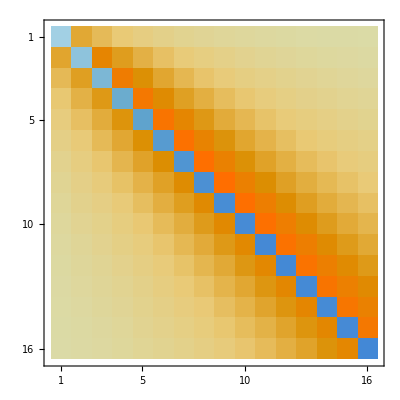

```mathematica
MatrixPlot[R]
```

```mathematica
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0],P11[0],P12[0],P13[0],P14[0],P15[0]}=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{P0→InterpolatingFunction[{{0.,0.01}},<>],P1→InterpolatingFunction[{{0.,0.01}},<>],P2→InterpolatingFunction[{{0.,0.01}},<>],P3→InterpolatingFunction[{{0.,0.01}},<>],P4→InterpolatingFunction[{{0.,0.01}},<>],P5→InterpolatingFunction[{{0.,0.01}},<>],P6→InterpolatingFunction[{{0.,0.01}},<>],P7→InterpolatingFunction[{{0.,0.01}},<>],P8→InterpolatingFunction[{{0.,0.01}},<>],P9→InterpolatingFunction[{{0.,0.01}},<>],P10→InterpolatingFunction[{{0.,0.01}},<>],P11→InterpolatingFunction[{{0.,0.01}},<>],P12→InterpolatingFunction[{{0.,0.01}},<>],P13→InterpolatingFunction[{{0.,0.01}},<>],P14→InterpolatingFunction[{{0.,0.01}},<>],P15→InterpolatingFunction[{{0.,0.01}},<>]}}

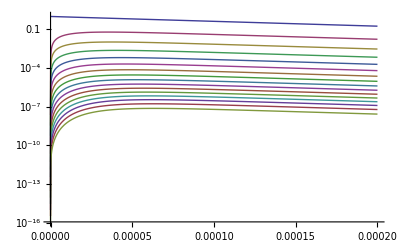

```mathematica
sol=NDSolve[LogicalExpand[Pm'[t]==R.Pm[t]&&init],Pmen,{t,0,0.01}]
LogPlot[Evaluate[{P0[t], P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]}/.sol],{t,0,0.0002}, PlotRange -> All, PlotLegend -> {0,1,2,3,4,5,6,7,8,9,10, 11,12,13,14, 15}, LegendShadow -> None]
```

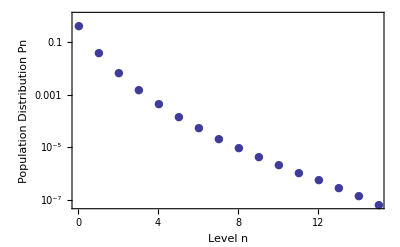

```mathematica
tel = 0.0001;
SteadyState = Table[
func = Pmen[[n+1]]/.First[sol];
steadyvalue = func[tel];
{n, steadyvalue},{n,0,15}];
ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"}]
```

```mathematica
SteadySum = Sum[func  = Pmen[[n+1]]/.First[sol];
func[tel], {n,0, nmax}];
NormalizedSteadyState =Table[{n,SteadyState[[n+1]][[2]] / SteadySum },{n,0,15}]
```

{{0,0.8938+0. ⅈ},{1,0.0862082+0. ⅈ},{2,0.0150322+0. ⅈ},{3,0.00346724+0. ⅈ},{4,0.000973437+0. ⅈ},{5,0.000317016+0. ⅈ},{6,0.000116164+0. ⅈ},{7,0.0000468616+0. ⅈ},{8,0.0000204503+0. ⅈ},{9,9.51112×10^-6+0. ⅈ},{10,4.64963×10^-6+0. ⅈ},{11,2.3557×10^-6+0. ⅈ},{12,1.21598×10^-6+0. ⅈ},{13,6.23419×10^-7+0. ⅈ},{14,3.01804×10^-7+0. ⅈ},{15,1.33301×10^-7+0. ⅈ}}

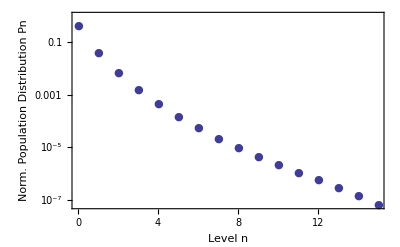

```mathematica
ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Norm. Population Distribution Pn"}]
```